## Test integral control + feedforward in state space (Ex. 4.11)

```mathematica
Clear["Global`*"]
```

```mathematica
G0 = TransferFunctionModel[1/(s+a),s];sys0 = StateSpaceModel[G0]
```

-a110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
kr1 = -1/(1(1/(-a-k))1) // Simplify
```

a+k

```mathematica
a1 = ({{-a-k, -ki}, {1, 0}}); b1 = ({{kr1}, {-1}}); c1 = ({{1, 0}});sys1 = StateSpaceModel[{a1,b1,c1}] /. { a-> 1 ,k->1 ,ki->0}
```

-20210-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
tmax=10;y1 = OutputResponse[sys1,UnitStep[t],t] [[1]]
```

ⅇ^(-2 t) (-1+ⅇ^(2 t)) UnitStep[t]

```mathematica
kr2 = 0; b2 =  ({{kr2}, {-1}});sys2 = StateSpaceModel[{a1,b2,c1}] /. { a-> 1 ,k->1 ,ki->1}
```

-2-1010-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
y2 = OutputResponse[sys2,UnitStep[t],t] [[1]]//Simplify
```

ⅇ^-t (-1+ⅇ^t-t) UnitStep[t]

```mathematica
{sys3 = StateSpaceModel[{a1,b1,c1}] /. { a-> 1 ,k->1 ,ki->1},
y3 = OutputResponse[sys3,UnitStep[t],t] [[1]]//Simplify}
```

{-2-1210-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,ⅇ^-t (-1+ⅇ^t+t) UnitStep[t]}

Now look at what happens when you have the wrong value of feedforward.  Assume a=1 but really is 2

```mathematica
kr4 =(k+a)/2; b4 = ({{kr4}, {-1}});
{sys4 = StateSpaceModel[{a1,b4,c1}] /.{ a-> 1 ,k->1 ,ki->0},
y4 = OutputResponse[sys4,UnitStep[t],t] [[1]]//Simplify}
```

{-20110-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,1/2 ⅇ^(-2 t) (-1+ⅇ^(2 t)) UnitStep[t]}

```mathematica
{sys5 = StateSpaceModel[{a1,b2,c1}] /. { a-> 1 ,k->1 ,ki->1},
y5 = OutputResponse[sys5,UnitStep[t],t] [[1]]//Simplify}
```

{-2-1010-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,ⅇ^-t (-1+ⅇ^t-t) UnitStep[t]}

```mathematica
{sys6 = StateSpaceModel[{a1,b4,c1}] /. { a-> 1 ,k->1 ,ki->1},
y6 = OutputResponse[sys6,UnitStep[t],t] [[1]]//Simplify}
```

{-2-1110-1100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,(1-ⅇ^-t) UnitStep[t]}

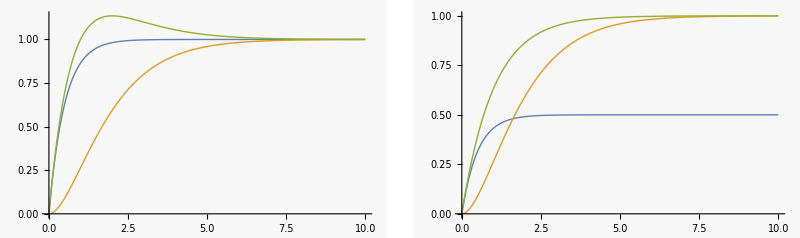

```mathematica
p1=Plot[{y1,y2,y3},{t,0,tmax},PlotRange->Full];
p2=Plot[{y4,y5,y6},{t,0,tmax},PlotRange->Full];
GraphicsRow[{p1,p2}]
```

Export data

```mathematica
dt=0.01;dat = Table[{y4,y5,y6},{t,0,tmax,dt}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["integralControlFF.dat", dat];
*)
```